```mathematica
DSolve[{t'[c]==-250000 Exp[10^-6 t[c]], t[5] == 0}, t[c], c]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t[c]→-1000000 Log[(-250000+250000 c)/1000000]}}

-1000000 Log[(-250000+250000 c)/1000000]

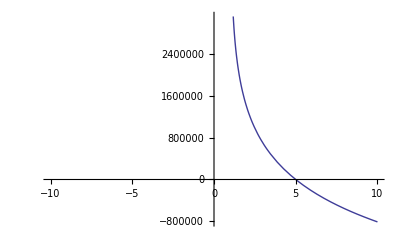

```mathematica
t[c_]=-1000000 Log[(-250000+250000 c)/1000000]
Plot[t[x], {x, -10, 10}]
```

```mathematica
t[2.5]
```

980829.